# 24: Eigenvalue Problems:

Eigenvalue eigenvector pairs of square matrices are next.  Your linear algebra class always wrote  
	A.v=λ v
your book likes to write A.x = λ x.  Whatever you want to call the eigenvector v it is important to realize that A is a map from a space into itself. An eigenvector is a special element of the space that preserves direction but not generally length under the map A.

For A∈ℂ^(m×m) any pair λ∈ℂ  and x∈ℂ^m (with ||x||≠0) satisfying
	A.x=λ x 
is an eigenpair for A: λ is the eigenvalue associated with the eigenvector ||x||.

The span of a set of eigenvectors is called an eigenspace.

The set of all eigenvalues Λ(A) of A is the spectrum.

Finding eigenpairs is a non-linear problem!

Physical resonances are described by spectra and eigenspace

Eigenspace let you “diagonalize” linear ODEs and other problems.

## Eigen Decomposition

With m linearly independent eigenvectors x_1,x_2,…,x_m you can define an invertible matrix
	X=[x_1 | | | x_2 | | | … | | | x_m]
which satisfies
	A.X=A.[x_1 | | | x_2 | | | … | | | x_m]=[A.x_1 | | | A.x_2 | | | … | | | A.x_m]=[λ_1 x_1 | | | λ_2 x_2 | | | … | | | λ_m x_m]
which is the same as
	A.X=X.Λ
where Λ is the diagonal matrix of eigenvalues.  This is called an eigen decomposition of A and is normally written
	A=X.Λ.X^-1
This says A is diagonal under a change of basis.  For real A this is only an orthogonal change of basis if A=Aᵀ.

## Geometric Multiplicity

One eigenvalue can have more than one linearly independent eigenvector.

The geometric multiplicity of an eigenvalue λ is the dimension of its eigenspace.

## Characteristic Polynomial

The characteristic polynomial of A is p_A(z)=det(z I - A)=z^m+…

Characteristic polynomial roots match eigenvalues

The algebraic multiplicity of an eigenvalue is the multiplicity of the characteristic polynomial root.

## Defective Eigenvalues and Matrices

An eigenvalue is defective if the multiplicities do not match.

A matrix is defective if it has a defective eigenvalue

Non-defective matrices have a full set of eigenvectors and are diagonalizable A=X.Λ.X^-1

The non-diagonalizable defective matrix 
	A=(3 | 1 | 0 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4)
Has three distinct eigenvalues 3,-2,4.

The eigenvalue 4 has geometric and algebraic multiplicity 2.

The eigenvalue -2 has geometric multiplicity 1 and algebraic multiplicity 2.

The eigenvalue 3 has geometric multiplicity 1 and algebraic multiplicity 3.

## Similarity Transformations

If Y∈ℂ^(m×m) is invertible the the eigenvalues of Y^-1.A.Y are the same as the eigenvalues of Y.

If there is a unitary Q satisfying Q.A.Q^H then is is unitarily diagonalizable.

A matrix A is normal if A^H.A=A.A^H.  Normal matrices are unitarily diagonalizable.

Hermitian matrices (A=A^H ) are unitarily diagonalizable and have real eigenvalues.

## Schur Factorization

All square matrices have a Schur factorization A=Q.T.Q^H into a product of a Unitary Q and an Upper Triangular T. The eigenvalues of T are exposed on the diagonal.!

## Locating Eigenvalues

There is a theorem that says that all the eigenvalues are within some disks.

“Every eigenvalue of A lies in at least one of the m circular disks with centers c_i=A⟦i,i⟧ and radius r_i=∑_(j≠i) |A⟦i,j⟧|. If n of the disks form a connected domain Ω disjoint from the other disks there are n eigenvalues in Ω.”

Here is a picture for the theorem.

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```

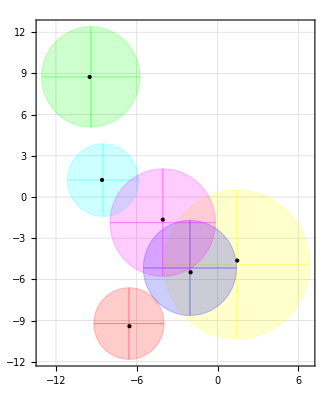

```mathematica
m=6;
A=RandomComplex[{-1-I,1+I},{m,m}]; A =A+10DiagonalMatrix[RandomComplex[{-1-1I,1+1 I},m]];
λs=Eigenvalues[A];
GershgorignPic[A]
```

## Computing Eigenvalues

We compute eigenvalues by building one of the above decompositions and reading off the eigenvalues.